# Contour Plot - implementation

## A contour plot for the energy function of triaxial rigid rotor

## The calculations are done for ^135Pr isotope. Triaxial nucleus in which wobbling motion is

## General formula for the energy function of the nucleus. H_rot=x_2^2+ux_3^2+2 v_0 x_2^2

## Inertial functions

```mathematica
Afct[spin_,oddspin_,a1_,a2_,th_]:=a2(1-(oddspin*Sin[th])/spin)-a1;
ufct[spin_,oddspin_,a1_,a2_,a3_,th_]:=(a3-a1)/Afct[spin,oddspin,a1,a2,th];
v0fct[spin_,oddspin_,a1_,a2_,th_]:=-(a1*oddspin*Cos[th])/Afct[spin,oddspin,a1,a2,th];
vfct[spin_,oddspin_,a1_,a2_,th_]:=v0fct[spin,oddspin,a1,a2,th]/spin;
```

## Constants

## The following parameters correspond to the case of 1-axis quantization, largest moment of inertia being the one of x_1 axis. The parameters are the one obtained from fitting the energies of the three wobbling bands.

```mathematica
I1=89;
I2=12;
I3=48;
THETA=N[-71*π/180];
SPIN=19/2;
j=N[11/2];
quantSpin=SPIN+2;
A1=1/(2*I1);
A2=1/(2*I2);
A3=1/(2*I3);
```

## Numerical values for the inertial parameters (u,v_0) based on the fixed parameter set

```mathematica
u[spin_]:=N[ufct[spin,j,A1,A2,A3,THETA]];
v0[spin_]:=N[v0fct[spin,j,A1,A2,THETA]];
k[spin_]:=N[√ufct[spin,j,A1,A2,A3,THETA]];
```

## New change of variable for Energy Function H_rot

## H_(rot(cart))=x_2^2+ux_3^2+2 v_0 x_1

## I^2=x_1^2+x_2^2+x_3^2

```mathematica
(*spinC - the current spin for which the plot is being evaluated at.*)
(*spinT - the maximum value for the spin*)
```

```mathematica
Hrot[spinC_,spinT_,x1_,x3_]:=spinT^2+(u[spinC]-1)x3^2-x1^2+2v0[spinC]x1;
```

```mathematica
Hrot[11.5,5,5]
```

82.6029

```mathematica
cp[spin_]:=ContourPlot[Hrot[spin,x1,x3],{x1,-spin,spin},{x3,-spin,spin}];
```

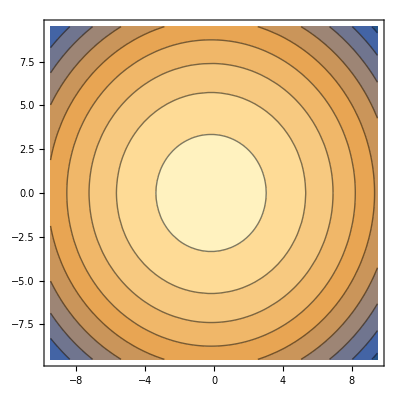

```mathematica
cp[SPIN]
```